## Utils

```mathematica
SetDirectory["C:\\Users\\drezn\\Dropbox\\Mathematica"];
```

```mathematica
toDeg[r_]:=180.*r/π;
toRad[d_]:=π*d/180.;
negl[v_]:=Abs[v]<10^-9;
magn2[v_]:=v.v;
magn[v_]:=Sqrt[magn2[v]];
flipY[{x_,y_}]:={x,-y};
flipX[{x_,y_}]:={-x,y};
perp[{x_,y_}]:={-y,x};
perpNeg[{x_,y_}]:={y,-x};
refl[v_,n_]:=2(v.n)n/magn2[n]-v;
norm[v_]:=v/magn[v];
clamp[v_,max_:100]:=If[v>max,max,If[v<-max,-max,v]];
ray[p0_,phat_,d_]:=p0+phat*d;
rot[p_,st_,ct_]:=Module[{m},
m={{ct,-st},{st,ct}};
m.p];
getEquilateral[th_]:=Module[{s=Sin[2π/3.],c=Cos[2π/3.]},
NestList[rot[#,s,c]&,rot[{1.,0.},Sin@th,Cos@th],2]];
(*x0+nx*t=0= >t=-x0/nx;*)
interY[p0_,phat_]:=Module[{t},
t=-p0[[1]]/phat[[1]];
ray[p0,phat,t]];
(*y0+ny*t=0= >t=-y0/ny;*)
interX[p0_,phat_]:=Module[{t},
t=-p0[[2]]/phat[[2]];
ray[p0,phat,t]];
```

-s (dl.dl)+(p-l1)dl==0⇒ s=(p-l1).dl/dl^2

```mathematica
closestPerp[p_,l1_,l2_]:=Module[{dl=l2-l1,s},
s=((p-l1).dl)/(dl.dl);
ray[l1,dl,s]];
```

```mathematica
Clear@quadRoots;
quadRoots[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
If[det<0,Print["quadRoots fail: {a,b,c}="<>ToString@{a,b,c}];False,
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)]];
Clear@interRays;
interRays[p1_,n1_,p2_,n2_]:=Module[{m,b,sols},
m=Transpose[{n1,n2}];(*{{nx1,-nx2},{ny1,-ny2}};*)
If[negl[Det[m]],p1,
b=p2-p1;(*{x2-x1,y2-y1}];*)
sols=LinearSolve[m,b];
ray[p1,n1,sols[[1]]]]
];
```

#### Ellipse

```mathematica
ellEqn[a_,x_,y_]:=(x/a)^2+y^2-1;
ellGrad[a_,x_,y_]:=-{x,y a^2};(* (x/a)^2+y^2==1 *)
ellY[a_,x_]:=Sqrt[1-(x/a)^2];
```

```mathematica
ellRayCoeffs=Module[{r,eqn,sols},
r=ray[{x,y},{nx,ny},s];
eqn=FullSimplify[ellEqn[a,r[[1]],r[[2]]],Assumptions->a>0&&Abs[x]<=a&&(nx^2+ny^2==1)];
FullSimplify[a^2 CoefficientList[eqn,s],a>0]]
```

{x^2+a^2 (-1+y^2),2 (nx x+a^2 ny y),nx^2+a^2 ny^2}

```mathematica
Clear@ellInterRay;
ellInterRay[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRoots[c2,c1,c0];
If[ListQ[ss],
ray[{x,y},{nx,ny},#]&/@ss,
{{x,y},{x,y}}]
];
```

Used for Proofs

```mathematica
quadRootsUnprot[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)];Clear@ellInterRayUnprot;
ellInterRayUnprot[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRootsUnprot[c2,c1,c0];
ray[{x,y},{nx,ny},#]&/@ss
];
```

```mathematica
Clear@triSides;triSides[vs_]:=MapThread[(#1-#2)&,{vs,RotateLeft@vs}];
Clear@triLengths;triLengths[vs_]:=magn/@triSides[vs];
triPer[tri_]:=Total[triLengths@tri];
(* a,b,c are side lengths *)
Clear@triAreaHeron;triAreaHeron[{a_,b_,c_}]:=Module[{s},
s=(a+b+c)/2;(* semi perimeter *)
Sqrt[s*(s-a)*(s-b)*(s-c)]];
```

## Ellipse Invariants

#### Constant Perimeter (Dabroux, 1917)

```mathematica
Clear[dabrouxP];dabrouxP[a_,b_:1]:=Module[{a2,b2,delta,per},
a2=a^2;
b2=b^2;
delta=Sqrt[a2^2-a2 b2+b2^2];
per=2Sqrt[2delta-a2-b2](a2+b2+delta)/(a2-b2);
per
];
```

#### Exit angle at x_1 which creates triangular orbit (Garcia, 2019)

-Graphics-

```mathematica
cosAlpha[a_,x_]:=Module[{x2,a2,a4,c2},
x2=x^2;
a2=a^2;
a4=a2^2;
c2=a2-1;
a2 Sqrt[-a2-1+2Sqrt[a4-c2]]/(c2 Sqrt[a4-c2 x2])];
```

```mathematica
cosAlpha[a,x]//TeXForm
```

\frac{a^2 \sqrt{-a^2+2 \sqrt{a^4-a^2+1}-1}}{\left(a^2-1\right) \sqrt{a^4-\left(a^2-1\right) x^2}}

#### Can I find an expression for the next orbit point P_2 in terms of “a” and x_1

```mathematica
getP2[a_,x1_]:=Module[{y,p1,norm,ca,sa,p2,normRot},
y=-ellY[a,x1];
p1={x1,y};
ca=cosAlpha[a,x1]/.{Sqrt[1-a^2+a^4]->d}/.{-1-a^2+2 d->d2};(* to simplify *)
sa=Sqrt[1-ca^2];
norm=ellGrad[a,x1,y];
normRot=rot[norm,sa,ca];
p2=ellInterRayUnprot[a,p1,normRot][[2]]; (* get 2nd solution *)
p2];
```

## Triangular Orbits

```mathematica
Clear@getReflData;getReflData [a_,p0_,normal_,sinAlpha_,cosAlpha_]:=Module[{nRot,inter,interNorm,interRefl,nextInter,nextInterNorm},
nRot=rot[normal,sinAlpha,cosAlpha];
inter=ellInterRay[a,p0,nRot][[2]];
interNorm=norm[ellGrad[a,inter[[1]],inter[[2]]]];
interRefl=refl[norm[p0-inter],interNorm];
nextInter=ellInterRay[a,inter,interRefl][[2]];
nextInterNorm=norm[ellGrad[a,nextInter[[1]],nextInter[[2]]]];
{ (* returns an "object" *)
"nRot"->nRot,
"inter"->inter,
"interNorm"->interNorm,
"interRefl"->interRefl,
"nextInter"->nextInter,
"nextInterNorm"->nextInterNorm
}];
```

```mathematica
Options[getOrbitData]={posY->False};Clear@getOrbitData;getOrbitData[a_,x_,OptionsPattern[]]:=Module[{y,o1,n1,ca,sa,sa2,ca2,halfAlpha,pos,neg},
y=-ellY[a,x];
If[OptionValue@posY,y=-y];
o1={x,y};
n1=norm[ellGrad[a,x,y]];
ca=cosAlpha[a,x];
sa=Sqrt[1-ca^2];
pos=getReflData[a,o1,n1,sa,ca];
neg=getReflData[a,o1,n1,-sa,ca];(* orbit at -α *)
(* half-angle to display α at bisector *)
sa2=Sqrt[(1-ca)/2];
ca2=Sqrt[(1+ca)/2];
halfAlpha=rot[n1,sa2,ca2];
{
"ca"->ca,
"sa"->sa,
"halfAlpha"->halfAlpha,
"nRot"->("nRot"/.pos),
"interRefl"->("interRefl"/.pos),
"orbit"->{o1,"inter"/.pos,"nextInter"/.pos},
"normals"->{n1,"interNorm"/.pos,"nextInterNorm"/.pos},
"nRotNeg"->("nRot"/.neg),
"interReflNeg"->("interRefl"/.neg),
"orbitNeg"->{o1,"inter"/.neg,"nextInter"/.neg},
"normalsNeg"->{n1,"interNorm"/.neg,"nextInterNorm"/.neg}
}
];
```

```mathematica
getOrbitData[2.,1.,posY->False]//ColumnForm
```

ca→0.549885
sa→0.835241
halfAlpha→{-0.699945,0.714197}
nRot→{-0.954984,0.296658}
interRefl→{0.999046,0.0436602}
orbit→{{1.,-0.866025},{-1.99582,0.0646022},{1.94314,0.236743}}
normals→{{-0.27735,0.960769},{0.991722,-0.128403},{-0.898933,-0.438085}}
nRotNeg→{0.649963,0.759966}
interReflNeg→{-0.999046,-0.0436602}
orbitNeg→{{1.,-0.866025},{1.94314,0.236743},{-1.99582,0.0646022}}
normalsNeg→{{-0.27735,0.960769},{-0.898933,-0.438085},{0.991722,-0.128403}}

```mathematica
Clear@orbitNormals;orbitNormals[a_,t_]:=Module[{ellP,orbitData},
ellP={N@a * Cos[N@t],Sin[N@t]};
orbitData=getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)];
{"orbit"/.orbitData,"normals"/.orbitData}
];
```

## Triangular (Notable) Points

#### Linha de Euler: bari, ortho, circum, 9-pc all lie on a line (but not incenter)

-Graphics-

```mathematica
(* order by oposition to vertices *)
getMedians[t1_,t2_,t3_]:={t2+t3,t1+t3,t1+t2}/2;
```

```mathematica
getAltBases[p1_,p2_,p3_]:=Module[{sides},
sides={{p2,p3},{p3,p1},{p1,p2}};
MapThread[closestPerp[#1,#2[[1]],#2[[2]]]&,{{p1,p2,p3},sides}]];
```

```mathematica
getIncenter[p1_,n1_,p2_,n2_]:=interRays[p1,n1,p2,n2];
Clear@getBaricenter;getBaricenter[p1_,p2_,p3_]:=Module[{medians},(*(p1+p2+p3)/3;*)
medians=getMedians[p1,p2,p3];
interRays[p1,medians[[1]](*23*)-p1,p2,medians[[2]](*31*)-p2]
];
getOrthocenter[p1_,p2_,p3_]:=Module[{altBases},
altBases=getAltBases[p1,p2,p3];
interRays[p1,altBases[[1]]-p1,p2,altBases[[2]]-p2]
];
getCircumcenter[p1_,p2_,p3_]:=Module[{medians,medianPerps},
medians=getMedians[p1,p2,p3];
medianPerps={
medians[[1]]+norm[perp[p2-p3]],
medians[[2]]+norm[perp[p3-p1]],
medians[[3]]+norm[perp[p1-p2]]
};
interRays[medians[[1]](*2+3*),perp[p2-p3],medians[[2]](*3+1*),perp[p1-p3]]
];
```

#### Nine Point Circle: its center is the circumcenter of the medians, and is tangent to incircle (at Feuerbach point) and all 3 excircles

-Graphics--Graphics-

```mathematica
getNinepointcenter[p1_,p2_,p3_]:=Module[{medians},
medians=getMedians[p1,p2,p3];
getCircumcenter@@medians
];
```

```mathematica
Clear@inRadius0;
inRadius0[incenter_,p1_,p2_]:=Module[{ctr,foot,d},
foot=closestPerp[incenter,p1,p2];
magn[incenter-foot]];
```

```mathematica
circumRadius0[circumcenter_,p1_]:=magn[circumcenter-p1];
```

```mathematica
(* shoot ray from incenter *)
getFeuerbachpoint[npc_,incenter_,inradius_]:=Module[{inter},
ray[incenter,norm[incenter-npc],inradius]
];
```

```mathematica
getExcenters[orbit_,normals_]:=Module[{perps,perpsNeg,exc},
perps=perp/@normals;
perpsNeg=perpNeg/@normals;
exc=MapThread[interRays[#1,#2,#3,#4]&,{orbit,perps,RotateLeft@orbit,RotateLeft@perpsNeg}];
exc];
```

#### Gergonne Point: perspector of ABC and its contact triangle Ta, Tb, Tc

## Triangular Points with Trilinears: X(1) ~ X(100) via R scraping

Trilinears x : y : z convert via triangle vertices A, B, C  and sides a, b, c :

```mathematica
Clear@trilinearToCartesian;
trilinearToCartesian[
{A_,B_,C_},(* vertices *)
{a_,b_,c_},(* side lengths *)
{x_,y_,z_} (* trilinears *)
]:=Module[{(*a,b,c,*)denom},
(* may not need *)
(*a=magn[C-B];b=magn[A-C];c=magn[B-A];*)
denom={a,b,c}.{x,y,z};
(a x A+b y B+c z C)/denom];
```

```mathematica
rotateSym[fabc_]:={fabc,fabc/.{a->b,b->c,c->a},fabc/.{a->c,b->a,c->b}}
```

```mathematica
(* trilinears: a:b:c *)
getIncenterTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,{1,1,1}];
getSymmedian[orbit_,sides_]:=trilinearToCartesian[orbit,sides,sides];
getMitten[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b+c-a,c+a-b,a+b-c}];
getGergonne[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b*c/(b+c-a),c*a/(c+a-b),a*b/(a+b-c)}];
getNagel[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c}, {(b+c-a)/a,(c+a-b)/b,(a+b-c)/c}];
getSpieker[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c(b+c),c a(c+a),a b (a+b)}];
getCentroid[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c,c a,a b}];
```

-Graphics-

```mathematica
(* gives cos(A) *)
lawOfCosines[a_,b_,c_]:=(b^2+c^2-a^2)/(2b c);
getSin[theCos_]:=Sqrt[1-theCos^2];
cosDoubleAngle[cosAngle_]:=2*cosAngle*cosAngle-1;
sinCosTripleAngle[s_,c_,s2_,c2_]:=Module[{s3,c3},
c3=c2 c-s2 s;
s3=s2 c+s c2;
{s3,c3}];
```

```mathematica
getSinCosApB[sa_,sb_,ca_,cb_]:={sa cb + sb ca ,ca cb - sa sb};
getSinCosAmB[sa_,sb_,ca_,cb_]:= {sa cb - sb ca,ca cb + sa sb};
getSinApmB[sa_,sb_,ca_,cb_]:= {sa cb + sb ca,sa cb - sb ca};
```

```mathematica
Clear@getNewCenters;
getNewCenters[orbit_,{a_,b_,c_},singles_:{}]:=Module[{eqns,
cosA,cosB,cosC,sinA,sinB,sinC,
secA,secB,secC,cscA,cscB,cscC,
tanA,tanB,tanC,cotA,cotB,cotC,
cos2A,cos2B,cos2C,sin2A,sin2B,sin2C,
sec2A,sec2B,sec2C,csc2A,csc2B,csc2C,
cos3A,sin3A,cos3B,sin3B,cos3C,sin3C,
sec3A,sec3B,sec3C,csc3A,csc3B,csc3C,
cPi3=Cos[π/3.],sPi3=Sin[π/3.],cPi6=Cos[π/6.],sPi6=Sin[π/6.],
sinApPi3,sinBpPi3,sinCpPi3,sinAmPi3,sinBmPi3,sinCmPi3,
sinApPi6,sinBpPi6,sinCpPi6,sinAmPi6,sinBmPi6,sinCmPi6,
cscApPi3,cscBpPi3,cscCpPi3,cscAmPi3,cscBmPi3,cscCmPi3,
cscApPi6,cscBpPi6,cscCpPi6,cscAmPi6,cscBmPi6,cscCmPi6},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{secA,secB,secC}=1/{cosA,cosB,cosC};
{cscA,cscB,cscC}=1/{sinA,sinB,sinC};
{tanA,tanB,tanC}={sinA,sinB,sinC}/{cosA,cosB,cosC};
{cotA,cotB,cotC}=1/{tanA,tanB,tanC};
{cos2A,cos2B,cos2C}=cosDoubleAngle/@{cosA,cosB,cosC};
{sec2A,sec2B,sec2C}=1/{cos2A,cos2B,cos2C};
{sin2A,sin2B,sin2C}=getSin/@{cos2A,cos2B,cos2C};
{csc2A,csc2B,csc2C}=1/{sin2A,sin2B,sin2C};
{sin3A,cos3A}=sinCosTripleAngle[sinA,cosA,sin2A,cos2A];
{sin3B,cos3B}=sinCosTripleAngle[sinB,cosB,sin2B,cos2B];
{sin3C,cos3C}=sinCosTripleAngle[sinC,cosC,sin2C,cos2C];
{sec3A,sec3B,sec3C}=1/{cos3A,cos3B,cos3C};
{csc3A,csc3B,csc3C}=1/{sin3A,sin3B,sin3C};
{sinApPi3,sinAmPi3}=getSinApmB[sinA,sPi3,cosA,cPi3];
{sinBpPi3,sinBmPi3}=getSinApmB[sinB,sPi3,cosB,cPi3];
{sinCpPi3,sinCmPi3}=getSinApmB[sinC,sPi3,cosC,cPi3];
{sinApPi6,sinAmPi6}=getSinApmB[sinA,sPi6,cosA,cPi6];
{sinBpPi6,sinBmPi6}=getSinApmB[sinB,sPi6,cosB,cPi6];
{sinCpPi6,sinCmPi6}=getSinApmB[sinC,sPi6,cosC,cPi6];
{cscApPi3,cscBpPi3,cscCpPi3}=1/{sinApPi3,sinBpPi3,sinCpPi3};
{cscAmPi3,cscBmPi3,cscCmPi3}=1/{sinAmPi3,sinBmPi3,sinCmPi3};
{cscApPi6,cscBpPi6,cscCpPi6}=1/{sinApPi6,sinBpPi6,sinCpPi6};
{cscAmPi6,cscBmPi6,sinCmPi6}=1/{sinAmPi6,sinBmPi6,cscCmPi6};
eqns={
{"X(1)",Hold@{1,1,1},"INCENTER"},
{"X(2)",Hold@{b c,c a,a b},"CENTROID"},
{"X(3)",Hold@{cosA,cosB,cosC},"CIRCUMCENTER"},
{"X(4)",Hold@{secA,secB,secC},"ORTHOCENTER"},
{"X(5)",Hold@{cosB cosC+sinB sinC,cosC cosA+sinC sinA,cosA cosB+sinA sinB},"NINE-POINT CENTER"},{"X(6)",Hold@{a,b,c},"SYMMEDIAN / LEMOINE / GREBE POINT"},
{"X(7)",Hold@{b c/(b+c-a),c a/(c+a-b),a b/(a+b-c)},"GERGONNE POINT"},
{"X(8)",Hold@{(b+c-a)/a,(c+a-b)/b,(a+b-c)/c},"NAGEL POINT"},
{"X(9)",Hold@{b+c-a,c+a-b,a+b-c},"MITTENPUNKT"},
{"X(10)",Hold@{b c(b+c),c a(c+a),a b(a+b)},"SPIEKER CENTER"},{"X(11)",Hold@{1-cosB cosC+sinB sinC,1-cosC cosA+sinC sinA,1-cosA cosB+sinA sinB},"FEUERBACH POINT"},
{"X(12)",Hold@{1+cosB cosC+sinB sinC,1+cosC cosA+sinC sinA,1+cosA cosB+sinA sinB},"{X(1),X(5)}-HARMONIC CONJUGATE OF X(11)"},{"X(13)",Hold@{cscApPi3,cscBpPi3,cscCpPi3},"1st ISOGONIC CENTER (FERMAT / TORRICELLI POINT)"},{"X(14)",Hold@{cscAmPi3,cscBmPi3,cscCmPi3},"2nd ISOGONIC CENTER"},
{"X(15)",Hold@{sinApPi3,sinBpPi3,sinCpPi3},"1st ISODYNAMIC POINT"},
{"X(16)",Hold@{sinAmPi3,sinBmPi3,sinCmPi3},"2nd ISODYNAMIC POINT"},
{"X(17)",Hold@{cscApPi6,cscBpPi6,cscCpPi6},"1st NAPOLEON POINT"},
{"X(18)",Hold@{cscAmPi6,cscBmPi6,cscCmPi6},"2nd NAPOLEON POINT"},{"X(19)",Hold@{1/(b^2+c^2-a^2),1/(a^2+c^2-b^2),1/(a^2+b^2-c^2)},"CLAWSON POINT"},{"X(20)",Hold@{cosA-cosB cosC,cosB-cosC cosA,cosC-cosA cosB},"DE LONGCHAMPS POINT"},{"X(21)",Hold@{(b+c-a)/(b+c),(a+c-b)/(a+c),(a+b-c)/(a+b)},"SCHIFFLER POINT"},{"X(22)",Hold@{a(b^4+c^4-a^4),b(c^4+a^4-b^4),c(a^4+b^4-c^4)},"EXETER POINT"},{"X(23)",Hold@{a(b^4+c^4-a^4-b^2 c^2),b(a^4+c^4-b^4-a^2 c^2),c(b^4+a^4-c^4-b^2 a^2)},"FAR-OUT POINT"},{"X(24)",Hold@{secA cos2A,secB cos2B,secC cos2C},"PERSPECTOR OF ABC AND ORTHIC-OF-ORTHIC TRIANGLE"},{"X(25)",Hold@{a/(b^2+c^2-a^2),b/(c^2+a^2-b^2),c/(a^2+b^2-c^2)},"HOMOTHETIC CENTER OF ORTHIC AND TANGENTIAL TRIANGLES"},
{"X(26)",Hold@{a(b^2 cos2B+c^2 cos2C-a^2 cos2A),b(a^2 cos2A+c^2 cos2C-b^2 cos2B),c(a^2 cos2A+b^2 cos2B-c^2 cos2C)},"CIRCUMCENTER OF THE TANGENTIAL TRIANGLE"},
{"X(27)",Hold@{secA/(b+c),secB/(c+a),secC/(a+b)},"CEVAPOINT OF ORTHOCENTER AND CLAWSON CENTER"},{"X(28)",Hold@{tanA/(b+c),tanB/(c+a),tanC/(a+b)},"CEVAPOINT OF X(19) AND X(25)"},{"X(29)",Hold@{secA/(cosB+cosC),secB/(cosC+cosA),secC/(cosA+cosB)},"CEVAPOINT OF INCENTER AND ORTHOCENTER"},
{"X(30)",Hold@{cosA-2 cosB cosC,cosB-2 cosC cosA,cosC-2 cosA cosB},"EULER INFINITY POINT"},
{"X(31)",Hold@{a^2,b^2,c^2},"2nd POWER POINT"},
{"X(32)",Hold@{a^3,b^3,c^3},"3rd POWER POINT"},
{"X(33)",Hold@{1+secA,1+secB,1+secC},"PERSPECTOR OF THE ORTHIC AND INTANGENTS TRIANGLES"},{"X(34)",Hold@{1-secA,1-secB,1-secC},"X(4)-BETH CONJUGATE OF X(4)"},{"X(35)",Hold@{1+2 cosA,1+2 cosB,1+2 cosC},"{X(1),X(3)}-HARMONIC CONJUGATE OF X(36)"},{"X(36)",Hold@{1-2 cosA,1-2 cosB,1-2 cosC},"INVERSE-IN-CIRCUMCIRCLE OF INCENTER"},{"X(37)",Hold@{b+c,c+a,a+b},"CROSSPOINT OF INCENTER AND CENTROID"},{"X(38)",Hold@{b^2+c^2,c^2+a^2,a^2+b^2},"CROSSPOINT OF X(1) AND X(75)"},{"X(39)",Hold@{a(b^2+c^2),b(c^2+a^2),c(a^2+b^2)},"BROCARD MIDPOINT"},{"X(40)",Hold@{cosB+cosC-cosA-1,cosA+cosC-cosB-1,cosA+cosB-cosC-1},"BEVAN POINT"},
{"X(41)",Hold@{a^2(b+c-a),b^2(c+a-b),c^2(a+b-c)},"X(6)-CEVA CONJUGATE OF X(31)"},{"X(42)",Hold@{a(b+c),b(c+a),c(a+b)},"CROSSPOINT OF INCENTER AND SYMMEDIAN POINT"},{"X(43)",Hold@{a b+a c-b c,b c+b a-c a,c a+c b-a b},"X(6)-CEVA CONJUGATE OF X(1)"},{"X(44)",Hold@{b+c-2a,c+a-2b,a+b-2c},"X(6)-LINE CONJUGATE OF X(1)"},{"X(45)",Hold@{2b+2c-a,2c+2a-b,2a+2b-c},"X(9)-BETH CONJUGATE OF X(1)"},{"X(46)",Hold@{cosB+cosC-cosA,cosA+cosC-cosB,cosA+cosB-cosC},"X(4)-CEVA CONJUGATE OF X(1)"},{"X(47)",Hold@{cos2A,cos2B,cos2C},"X(110)-BETH CONJUGATE OF X(34)"},{"X(48)",Hold@{tanB+tanC,tanA+tanC,tanA+tanB},"CROSSPOINT OF X(1) AND X(63)"},{"X(49)",Hold@{cos3A,cos3B,cos3C},"CENTER OF SINE-TRIPLE-ANGLE CIRCLE"},
{"X(50)",Hold@{sin3A,sin3B,sin3C},"X(74)-CEVA CONJUGATE OF X(184)"},
{"X(51)",Hold@{a^2 (cosB cosC+sinB sinC),b^2 (cosC cosA+sinC sinA),c^2 (cosA cosB+sinA sinB)},"CENTROID OF ORTHIC TRIANGLE"},{"X(52)",Hold@{cos2A (cosB cosC+sinB sinC),cos2B (cosC cosA+sinC sinA),cos2C (cosA cosB+sinA sinB)},"ORTHOCENTER OF ORTHIC TRIANGLE"},{"X(53)",Hold@{tanA (cosB cosC+sinB sinC),tanB (cosC cosA+sinC sinA),tanC (cosA cosB+sinA sinB)},"SYMMEDIAN POINT OF ORTHIC TRIANGLE"},{"X(54)",Hold@{1/(cosB cosC+sinB sinC),1/(cosC cosA+sinC sinA),1/(cosA cosB+sinA sinB)},"KOSNITA POINT"},{"X(55)",Hold@{a(b+c-a),b(c+a-b),c(a+b-c)},"INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)"},{"X(56)",Hold@{a/(b+c-a),b/(c+a-b),c/(a+b-c)},"EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)"},{"X(57)",Hold@{1/(b+c-a),1/(c+a-b),1/(a+b-c)},"ISOGONAL CONJUGATE OF X(9)"},{"X(58)",Hold@{a/(b+c),b/(c+a),c/(a+b)},"ISOGONAL CONJUGATE OF X(10)"},
{"X(59)",Hold@{1/(1-(cosB cosC+sinB sinC)),1/(1-(cosC cosA+sinC sinA)),1/(1-(cosA cosB+sinA sinB))},"ISOGONAL CONJUGATE OF X(11)"},{"X(60)",Hold@{1/(1+(cosB cosC+sinB sinC)),1/(1+(cosC cosA+sinC sinA)),1/(1+(cosA cosB+sinA sinB))},"ISOGONAL CONJUGATE OF X(12)"},{"X(61)",Hold@{(sinA cPi6+sPi6 cosA),(sinB cPi6+sPi6 cosB),(sinC cPi6+sPi6 cosC)},"ISOGONAL CONJUGATE OF X(17)"},{"X(62)",Hold@{(sinA cPi6-sPi6 cosA),(sinB cPi6-sPi6 cosB),(sinC cPi6-sPi6 cosC)},"ISOGONAL CONJUGATE OF X(18)"},
{"X(63)",Hold@{cotA,cotB,cotC},"ISOGONAL CONJUGATE OF X(19)"},
{"X(64)",Hold@{1/(cosA-cosB cosC),1/(cosB-cosC cosA),1/(cosC-cosA cosB)},"ISOGONAL CONJUGATE OF X(20)"},{"X(65)",Hold@{cosB+cosC,cosC+cosA,cosA+cosB},"ORTHOCENTER OF THE INTOUCH TRIANGLE"},
{"X(66)",Hold@{b c/(b^4+c^4-a^4),c a/(c^4+a^4-b^4),a b/(a^4+b^4-c^4)},"ISOGONAL CONJUGATE OF X(22)"},{"X(67)",Hold@{b c/(b^4+c^4-a^4-b^2 c^2),c a/(c^4+a^4-b^4-c^2 a^2),a b/(a^4+b^4-c^4-a^2 b^2)},"ISOGONAL CONJUGATE OF X(23)"},{"X(68)",Hold@{cosA sec2A,cosB sec2B,cosC sec2C},"PRASOLOV POINT"},{"X(69)",Hold@{(cosA)/a^2,(cosB)/b^2,(cosC)/c^2},"SYMMEDIAN POINT OF THE ANTICOMPLEMENTARY TRIANGLE"},
{"X(70)",Hold@{b c/(b^2 cos2B+c^2 cos2C-a^2 cos2A),c a/(c^2 cos2C+a^2 cos2A-b^2 cos2B),a b/(a^2 cos2A+b^2 cos2B-c^2 cos2C)},"ISOGONAL CONJUGATE OF X(26)"},
{"X(71)",Hold@{(b+c) cosA,(c+a) cosB,(a+b) cosC},"ISOGONAL CONJUGATE OF X(27)"},{"X(72)",Hold@{(b+c) cotA,(c+a) cotB,(a+b) cotC},"ISOGONAL CONJUGATE OF X(28)"},{"X(73)",Hold@{secB+secC,secC+secA,secA+secB},"CROSSPOINT OF INCENTER AND CIRCUMCENTER"},
{"X(74)",Hold@{1/(cosA-2 cosB cosC),1/(cosB-2 cosC cosA),1/(cosC-2 cosA cosB)},"ISOGONAL CONJUGATE OF EULER INFINITY POINT"},{"X(75)",Hold@{1/a^2,1/b^2,1/c^2},"ISOTOMIC CONJUGATE OF INCENTER"},
{"X(76)",Hold@{1/a^3,1/b^3,1/c^3},"3rd BROCARD POINT"},
{"X(77)",Hold@{1/(1+secA),1/(1+secB),1/(1+secC)},"ISOGONAL CONJUGATE OF X(33)"},{"X(78)",Hold@{1/(1-secA),1/(1-secB),1/(1-secC)},"ISOGONAL CONJUGATE OF X(34)"},{"X(79)",Hold@{1/(1+2 cosA),1/(1+2 cosB),1/(1+2 cosC)},"ISOGONAL CONJUGATE OF X(35)"},{"X(80)",Hold@{1/(1-2 cosA),1/(1-2 cosB),1/(1-2 cosC)},"REFLECTION OF INCENTER IN FEUERBACH POINT"},{"X(81)",Hold@{1/(b+c),1/(c+a),1/(a+b)},"CEVAPOINT OF INCENTER AND SYMMEDIAN POINT"},
{"X(82)",Hold@{1/(b^2+c^2),1/(c^2+a^2),1/(a^2+b^2)},"ISOGONAL CONJUGATE OF X(38)"},{"X(83)",Hold@{b c/(b^2+c^2),a c/(c^2+a^2),a b/(a^2+b^2)},"CEVAPOINT OF CENTROID AND SYMMEDIAN POINT"},{"X(84)",Hold@{1/(cosB+cosC-cosA-1),1/(cosA+cosC-cosB-1),1/(cosA+cosB-cosC-1)},"ISOGONAL CONJUGATE OF X(40)"},
{"X(85)",Hold@{b^2 c^2/(b+c-a),c^2 a^2/(c+a-b),a^2 b^2/(a+b-c)},"ISOTOMIC CONJUGATE OF X(9)"},{"X(86)",Hold@{(b c)/(b+c),(c a)/(c+a),(a b)/(a+b)},"CEVAPOINT OF INCENTER AND CENTROID"},
{"X(87)",Hold@{1/(a b+a c-b c),1/(b c+b a-c a),1/(c a+c b-a b)},"X(2)-CROSS CONJUGATE OF X(1)"},
(* drawing billiard *)
{"X(88)",Hold@{1/(b+c-2a),1/(c+a-2b),1/(a+b-2c)},"ISOGONAL CONJUGATE OF X(44)"},{"X(89)",Hold@{1/(2b+2c-a),1/(2c+2a-b),1/(2a+2b-c)},"ISOGONAL CONJUGATE OF X(45)"},{"X(90)",Hold@{1/(cosB+cosC-cosA),1/(cosC+cosA-cosB),1/(cosA+cosB-cosC)},"X(3)-CROSS CONJUGATE OF X(1)"},
{"X(91)",Hold@{sec2A,sec2B,sec2C},"ISOGONAL CONJUGATE OF X(47)"},
{"X(92)",Hold@{csc2A,csc2B,csc2C},"CEVAPOINT OF INCENTER AND CLAWSON POINT"},
{"X(93)",Hold@{sec3A,sec3B,sec3C},"ISOGONAL CONJUGATE OF X(49)"},
{"X(94)",Hold@{csc3A,csc3B,csc3C},"ISOGONAL CONJUGATE OF X(50)"},{"X(95)",Hold@{b^2 c^2 1/(cosB cosC+sinB sinC),c^2 a^2 1/(cosC cosA+sinC sinA),a^2 b^2 1/(cosA cosB+sinA sinB)},"CEVAPOINT OF CENTROID AND CIRCUMCENTER"},{"X(96)",Hold@{sec2A 1/(cosB cosC+sinB sinC),sec2B 1/(cosC cosA+sinC sinA),sec2C 1/(cosA cosB+sinA sinB)},"ISOGONAL CONJUGATE OF X(52)"},{"X(97)",Hold@{cotA 1/(cosB cosC+sinB sinC),cotB 1/(cosC cosA+sinC sinA),cotC 1/(cosA cosB+sinA sinB)},"ISOGONAL CONJUGATE OF X(53)"},{"X(98)",Hold@{b c/(b^4+c^4-a^2 b^2-a^2 c^2),c a/(c^4+a^4-b^2 c^2-b^2 a^2),a b/(a^4+b^4-c^2 a^2-c^2 b^2)},"TARRY POINT"},
{"X(99)",Hold@{(b c)/(b^2-c^2),(c a)/(c^2-a^2),(a b)/(a^2-b^2)},"STEINER POINT"},{"X(100)",Hold@{1/(b-c),1/(c-a),1/(a-b)},"ANTICOMPLEMENT OF FEUERBACH POINT"}
};
Chop[{
#[[1]],#[[3]],
trilinearToCartesian[orbit,{a,b,c},ReleaseHold[#[[2]]]]}&/@
(* if singles ≠ {}, use the list to only evaluate requested indices *)
If[Length[singles]>0,eqns[[singles]],eqns]]
];
```

```mathematica
Clear@newCenters;newCenters[a_,t_,singles_:{}]:=Module[{orbit,normals,sides},
{orbit,normals}=orbitNormals[a,t];
orbit=Reverse@orbit;
sides=RotateLeft[triLengths[orbit]];
getNewCenters[orbit,sides,singles]
];
```

```mathematica
Clear@newCentersExc;newCentersExc[a_,t_,singles_:{}]:=Module[{orbit,normals,exc,sides},
{orbit,normals}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];
sides=RotateLeft@triLengths[exc];
getNewCenters[exc,sides,singles]
];
```

```mathematica
Clear@newCentersOrthic;newCentersOrthic[a_,t_,singles_:{}]:=Module[{orbit,normals,feet,sides},
{orbit,normals}=orbitNormals[a,t];
feet=getAltBases@@orbit;
sides=RotateLeft@triLengths[feet]; (* rotate left? *)
getNewCenters[feet,sides,singles]
];
```

```mathematica
Clear@newCentersMedial;newCentersMedial[a_,t_,singles_:{}]:=Module[{orbit,normals,meds,sides},
{orbit,normals}=orbitNormals[a,t];
meds=getMedians@@orbit;
sides=RotateLeft@triLengths[meds]; (* rotate left? *)
getNewCenters[meds,sides,singles]
];
```

## Loci Tables

```mathematica
Clear@getLociTable;
getLociTable[a_,ctrFn_,step_:toRad@.1]:=Module[{nc,pts,labs,loci},
loci=Table[
nc=ctrFn[a,t]//Quiet;
pts=(#[[3]]&/@nc);
{t,pts},
{t,.5*step,2.π,step}];
Transpose[#[[2]]&/@loci]];
```

```mathematica
doLociTables=True;
If[doLociTables,
loci15t=getLociTable[1.5,newCenters];
lociExc15t=getLociTable[1.5,newCentersExc];
lociOrt15t=getLociTable[1.5,newCentersOrthic];
lociMed15t=getLociTable[1.5,newCentersMedial];
];
```

*** GENERATES BILLIARD
X(100)  ANTICOMPLEMENT OF FEUERBACH POINT IS THE BILLIARD

*** GENERATES BILLIARD
X(88) = ISOGONAL CONJUGATE OF X(44)

X(44) = X(6)-LINE CONJUGATE OF X(1)
*** X(44) lies on these lines:
Trilinears       b + c - 2a : c + a - 2b : a + b - 2c
Barycentrics  a(b + c - 2a) : b(c + a - 2b) : c(a + b - 2c)
X(44) = (3r2 + 6rR + s2)*X(1) - 18rR*X(2) - 6r2*X(3)    (Peter Moses, April 2, 2013)

LINE-CONJUGATE: (looked up glossary)
Let P = p : q : r, U = u : v : w
The P-line conjugate of U is the point of intersection of line PU and the trilinear polar of the isogonal conjugate of U.

I.e., intersect line X(6)X(1) with the trilinear polar (TP) of the isog conjugate of X(1) which is X(1) itself.

The TP of X(1) is L1, the antiorthic axis, i.e., the orthic axis of the excentral triangle.

the orthic axis of a triangle are give by points (Oa, Ob,Oc) where each side of the orthic triangle meet the triangle sides (Oa, Ob, Oc)

-Graphics-
*** to summarize:

1) to get X(44) intersect the line connecting the incenter X(1) and the symmedian point X(6) with the orthic axis of the extriangle.
2) to get X(88) which generates the billiard, get the isogonal conjugate of X(44).

```mathematica
Clear@showLoci;showLoci[locus_,a_,locit_,lociExct_,lociOrtt_,lociMedt_,auto_,range_,imgSize_:400]:=Module[{nc,ncExc,ncOrt,ll,llexc,llort,ell,name,lociMaxX,maxX,lociMaxY,maxY,pts},
ell=plotEll[a];
nc=newCenters[a,0.0001,{locus}];
ncExc=newCentersExc[a,0.0001,{locus}];
ncOrt=newCentersOrthic[a,0.0001,{locus}];
pts={PointSize@Medium,Blue,Point[nc[[1,3]]],Green,Point[ncExc[[1,3]]],Red,Point[ncOrt[[1,3]]]};
name=nc[[1,1]]<>": " <>nc[[1,2]];
lociMaxX=clamp/@Table[Max[Select[Join[{a},First/@locit[[l]],First/@lociExct[[l]],First/@lociOrtt[[l]] ],NumberQ]],{l,1,Length@locit}];
lociMaxY=clamp/@Table[Max[Select[Join[{1},#[[2]]&/@locit[[l]],#[[2]]&/@lociExct[[l]],#[[2]]&/@lociOrtt[[l]] ],NumberQ]],{l,1,Length@locit}];
ll=ListLinePlot[locit[[locus]],ClippingStyle->None,PlotStyle->Blue];
llexc=ListLinePlot[lociExct[[locus]],ClippingStyle->None,PlotStyle->Green];
llort=ListLinePlot[lociOrtt[[locus]],ClippingStyle->None,PlotStyle->Red];
{maxX,maxY}=If[auto,
{lociMaxX[[locus]],lociMaxY[[locus]]},
{range,range}];
Show[{ell,ll,llexc,llort,Graphics@pts},ImageSize->{imgSize,imgSize},
Axes->True,PlotLabel->Style[name,Directive[{Black,14}]],PlotRange->{{-maxX,maxX},{-maxY,maxY}}]];
```

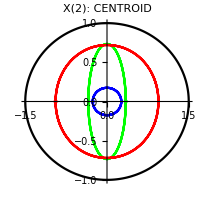

```mathematica
showLoci[2,1.5,loci15t,lociExc15t,lociOrt15t,True,2,200]
```

```mathematica
Manipulate[showLoci[locus,1.5,loci15t,lociExc15t,auto,range,500],
{{locus,1},1,Length@loci15t,1,Appearance->"Open"},(*important: 26,30,39exc,41exc,50,56exc-almost_circle,89exc-almost_point,92-pillow,100-retraces_ellipse*)
{{auto,True},{True,False}},
{{range,2},{1,2,4,8,16}}]
```

Part::partd: Part specification True ⟦ 1 ⟧ is longer than depth of object.

First::normal: Nonatomic expression expected at position 1 in First[True].

First::normal: Nonatomic expression expected at position 1 in First[1].

Part::pkspec1: The expression First[1] cannot be used as a part specification.

Join::heads: Heads List and Part at positions 1 and 4 are expected to be the same.

Part::partd: Part specification True ⟦ 2 ⟧ is longer than depth of object.

First::normal: Nonatomic expression expected at position 1 in First[True].

General::stop: Further output of First :: normal will be suppressed during this calculation.

Part::pkspec1: The expression First[2] cannot be used as a part specification.

Join::heads: Heads List and Part at positions 1 and 4 are expected to be the same.

Part::partd: Part specification True ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pkspec1: The expression First[3] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Join::heads: Heads List and Part at positions 1 and 4 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

ListLinePlot::lpn: True ⟦ 1 ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

Set::shape: Lists {maxX$91497546, maxY$91497546} and If[2, {lociMaxX$91497546 ⟦ 1 ⟧, lociMaxY$91497546 ⟦ 1 ⟧}, {500, 500}] are not the same shape.

Show::gcomb: Could not combine the graphics objects in ….

Part::partd: Part specification True ⟦ 1 ⟧ is longer than depth of object.

First::normal: Nonatomic expression expected at position 1 in First[True].

First::normal: Nonatomic expression expected at position 1 in First[1].

Part::pkspec1: The expression First[1] cannot be used as a part specification.

Join::heads: Heads List and Part at positions 1 and 4 are expected to be the same.

Part::partd: Part specification True ⟦ 2 ⟧ is longer than depth of object.

First::normal: Nonatomic expression expected at position 1 in First[True].

General::stop: Further output of First :: normal will be suppressed during this calculation.

Part::pkspec1: The expression First[2] cannot be used as a part specification.

Join::heads: Heads List and Part at positions 1 and 4 are expected to be the same.

Part::partd: Part specification True ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::pkspec1: The expression First[3] cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Join::heads: Heads List and Part at positions 1 and 4 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

ListLinePlot::lpn: True ⟦ 1 ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

Set::shape: Lists {maxX$91504653, maxY$91504653} and If[2, {lociMaxX$91504653 ⟦ 1 ⟧, lociMaxY$91504653 ⟦ 1 ⟧}, {500, 500}] are not the same shape.

Show::gcomb: Could not combine the graphics objects in ….

### X(56) = EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE) = a/(b + c - a) : b/(c + a - b) : c/(a + b - c) NEARLY CIRCULAR

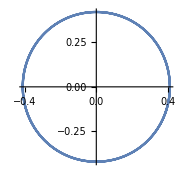

```mathematica
ListLinePlot[{lociExc15t[[56]]},AspectRatio->1,ImageSize->Small]
```

```mathematica
#[(magn/@lociExc15t[[56]])]&/@{Min,Max,Mean,StandardDeviation}
```

{0.412388,0.420736,0.417422,0.00297882}

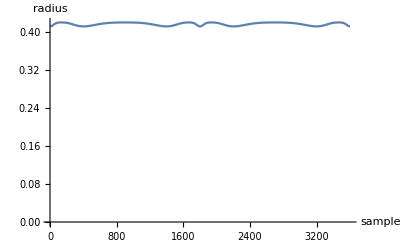

```mathematica
ListLinePlot[magn/@lociExc15t[[56]],AxesOrigin->{0,0},AxesLabel->{"sample","radius"}]
```

```mathematica
createLociFrames=False;If[createLociFrames,showLociFrames=Table[showLoci[locus,1.5,loci15t,lociExc15t,True,2,500],{locus,1,Length@loci15t,1}]];
```

```mathematica
Length@showLociFrames
```

0

```mathematica
Directory[]
```

C:\Users\drezn\Documents

```mathematica
Clear@padZ;padZ[v_,n_:4]:=ToString@NumberForm[v,{n,0},NumberPadding->{"0",""},NumberPoint->""];
getLocusFname[i_]:="loci/locus_"<>padZ[i]<>".png";
```

```mathematica
If[createLociFrames,MapIndexed[Export[getLocusFname[First[#2]],#1]&,showLociFrames]];
```